```mathematica
Import["ToMatlab.m","Package"]
```

# Supporting Information Sec 3.5 Considering relaxation, a general density function AA-Graphics- AB -Graphics- are used

## AA triangle Eq. S15

```mathematica
ClearAll["Global`*"]
```

```mathematica
fA[x_,y_,λ_,n_]=(Cos[(4 π x n)/(√3 λ)]+2 Cos[(2 π x n)/(√3 λ)] Cos[(2 π y n)/λ])
```

Cos[(4 n π x)/(√3 λ)]+2 Cos[(2 n π x)/(√3 λ)] Cos[(2 n π y)/λ]

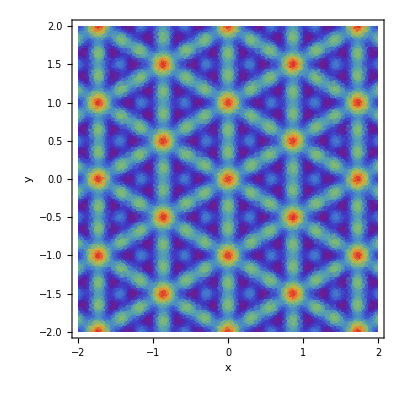

```mathematica
DensityPlot[Sum[fA[x,y,1,n],{n,3}],{x,-2,2},{y,-2,2},AxesLabel->Automatic, ColorFunction->"Rainbow",MaxRecursion->3]
```

```mathematica
λ0=as/(2*(1-Cos[θ]))^(1/2)
```

as/(√2 √(1-Cos[θ]))

```mathematica
f0AA[x_,y_,as_,θ_,n_]=fA[x,y,λ0,n]
```

Cos[(4 √(2/3) n π x √(1-Cos[θ]))/as]+2 Cos[(2 √(2/3) n π x √(1-Cos[θ]))/as] Cos[(2 √2 n π y √(1-Cos[θ]))/as]

```mathematica
nRf0AA[x_,y_,as_,θ_,R_,n_]=f0AA[x R,y R,as,θ,n]
```

Cos[(4 √(2/3) n π R x √(1-Cos[θ]))/as]+2 Cos[(2 √(2/3) n π R x √(1-Cos[θ]))/as] Cos[(2 √2 n π R y √(1-Cos[θ]))/as]

```mathematica
nRnasnareauf0AA[x_,y_,θ_,r_,n_]=Simplify[nRf0AA[x,y,as,θ,r*as,n]]
```

Sin[1/6 π (3-8 n r x √(6-6 Cos[θ]))]+2 Cos[2 n π r y √(2-2 Cos[θ])] Sin[1/6 π (3-4 n r x √(6-6 Cos[θ]))]

```mathematica
triarea=Integrate[Boole[y+Sqrt[3]x<1 &&y<Sqrt[3]x+1&& y>-1/2],{x,-1,1},{y,-1,1}]
```

(3 √3)/4

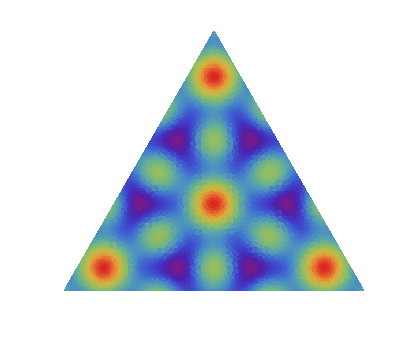

```mathematica
DensityPlot[Sum[nRnasnareauf0AA[x,y,1.5/180*Pi,30Sqrt[3],n],{n,2}],{x,-1,1},{y,-1,1},AxesLabel->Automatic, ColorFunction->"Rainbow",MaxRecursion->3, PlotRange->All,RegionFunction->Function[{x,y,z},y+Sqrt[3]x<1 &&y<Sqrt[3]x+1&& y>-1/2],AspectRatio->Automatic,Frame->False,FrameTicks->False]
```

```mathematica
t1=AbsoluteTime[];
triAA[θ_,r_,n_]=FullSimplify[Integrate[nRnasnareauf0AA[x,y,θ,r,n]Boole[y+Sqrt[3]x<1 &&y<Sqrt[3]x+1&& y>-1/2],{x,-1,1},{y,-1,1}] /triarea]
t2=AbsoluteTime[];
Print["time used ",(t2-t1)/60," mins" ]
```

-(3 Sin[n π r √(2-2 Cos[θ])]^2)/(2 n^2 π^2 r^2 (-1+Cos[θ]))

time used 0.27780455 mins

```mathematica
ToMatlab[triAA[theta,r,n]]
```

(-3/2).*n.^(-2).*pi.^(-2).*r.^(-2).*((-1)+cos(theta)).^(-1).*sin( ...
  n.*pi.*r.*(2+(-2).*cos(theta)).^(1/2)).^2;

## AB triangle Eq. S16

```mathematica
fB[x_,y_,λ_,n_]=(Cos[(4 π n(x-λ/√3))/(√3 λ)]+2 Cos[(2  π n(x-λ/√3))/(√3 λ)] Cos[(2  π y n)/λ])
```

2 Cos[(2 n π y)/λ] Cos[(2 n π (x-λ/(√3)))/(√3 λ)]+Cos[(4 n π (x-λ/(√3)))/(√3 λ)]

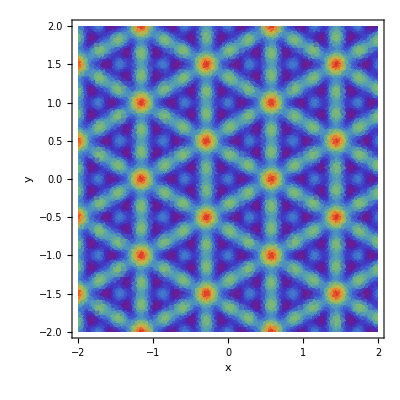

```mathematica
DensityPlot[Sum[fB[x,y,1,n],{n,3}],{x,-2,2},{y,-2,2},AxesLabel->Automatic, ColorFunction->"Rainbow",MaxRecursion->3]
```

```mathematica
λ0=as/(2*(1-Cos[θ]))^(1/2)
```

as/(√2 √(1-Cos[θ]))

```mathematica
f0AB[x_,y_,as_,θ_,n_]=fB[x,y,λ0,n]
```

2 Cos[(2 √2 n π y √(1-Cos[θ]))/as] Cos[(2 √(2/3) n π (x-as/(√6 √(1-Cos[θ]))) √(1-Cos[θ]))/as]+Cos[(4 √(2/3) n π (x-as/(√6 √(1-Cos[θ]))) √(1-Cos[θ]))/as]

```mathematica
nRf0AB[x_,y_,as_,θ_,R_,n_]=f0AB[x R,y R,as,θ,n]
```

2 Cos[(2 √2 n π R y √(1-Cos[θ]))/as] Cos[(2 √(2/3) n π (R x-as/(√6 √(1-Cos[θ]))) √(1-Cos[θ]))/as]+Cos[(4 √(2/3) n π (R x-as/(√6 √(1-Cos[θ]))) √(1-Cos[θ]))/as]

```mathematica
nRnasnareauf0AB[x_,y_,θ_,r_,n_]=Simplify[nRf0AB[x,y,as,θ,r*as,n]]
```

Cos[4/3 n π (-1+r x √(6-6 Cos[θ]))]+2 Cos[2/3 n π (-1+r x √(6-6 Cos[θ]))] Cos[2 n π r y √(2-2 Cos[θ])]

```mathematica
triarea=Integrate[Boole[y+Sqrt[3]x<1 &&y<Sqrt[3]x+1&& y>-1/2],{x,-1,1},{y,-1,1}]
```

(3 √3)/4

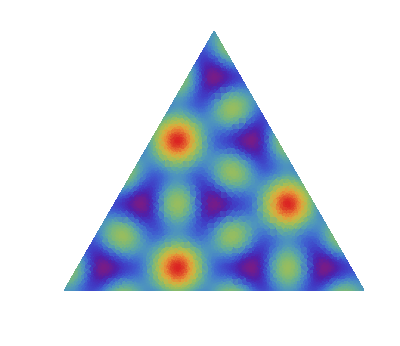

```mathematica
DensityPlot[Sum[nRnasnareauf0AB[x,y,1.5/180*Pi,30Sqrt[3],n],{n,2}],{x,-1,1},{y,-1,1},AxesLabel->Automatic, ColorFunction->"Rainbow",MaxRecursion->3, PlotRange->All,RegionFunction->Function[{x,y,z},y+Sqrt[3]x<1 &&y<Sqrt[3]x+1&& y>-1/2],AspectRatio->Automatic,Frame->False,FrameTicks->False]
```

```mathematica
t1=AbsoluteTime[];
triAB[θ_,r_,n_]=FullSimplify[Integrate[nRnasnareauf0AB[x,y,θ,r,n]Boole[y+Sqrt[3]x<1 &&y<Sqrt[3]x+1&& y>-1/2],{x,-1,1},{y,-1,1}] /triarea]
t2=AbsoluteTime[];
Print["time used ",(t2-t1)/60," mins" ]
```

-((2 Cos[(2 n π)/3]+Cos[(4 n π)/3]) Sin[n π r √(2-2 Cos[θ])]^2)/(2 n^2 π^2 r^2 (-1+Cos[θ]))

time used 0.53093983 mins

```mathematica
ToMatlab[triAB[theta,r,n]]
```

(-1/2).*n.^(-2).*pi.^(-2).*r.^(-2).*(2.*cos((2/3).*n.*pi)+cos(( ...
  4/3).*n.*pi)).*((-1)+cos(theta)).^(-1).*sin(n.*pi.*r.*(2+(-2).* ...
  cos(theta)).^(1/2)).^2;

## AA hexagon Eq. S17

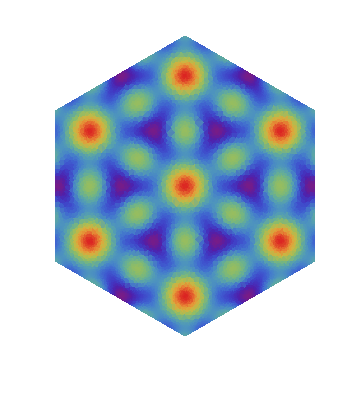

```mathematica
DensityPlot[Sum[nRnasnareauf0AA[x,y,1.5/180*Pi,30Sqrt[3],n],{n,2}],{x,-Sqrt[3]/2,Sqrt[3]/2},{y,-1,1},AxesLabel->Automatic, ColorFunction->"Rainbow",MaxRecursion->3, PlotRange->All,RegionFunction->Function[{x,y,z},-Sqrt[3]*x/3-1<y&&y<Sqrt[3]*x/3+1&&Sqrt[3]*x/3-1<y&&y<-Sqrt[3]*x/3+1],AspectRatio->Automatic,Frame->False,FrameTicks->False]
```

```mathematica
hexagonarea=Integrate[Boole[-Sqrt[3]*x/3-1<y&&y<Sqrt[3]*x/3+1&&Sqrt[3]*x/3-1<y&&y<-Sqrt[3]*x/3+1],{x,-Sqrt[3]/2,Sqrt[3]/2},{y,-1,1}]
```

(3 √3)/2

```mathematica
t1=AbsoluteTime[];
hexAA[θ_,r_,n_]=FullSimplify[Integrate[nRnasnareauf0AA[x,y,θ,r,n]Boole[-Sqrt[3]*x/3-1<y&&y<Sqrt[3]*x/3+1&&Sqrt[3]*x/3-1<y&&y<-Sqrt[3]*x/3+1],{x,-Sqrt[3]/2,Sqrt[3]/2},{y,-1,1}]/hexagonarea]
t2=AbsoluteTime[];
Print["time used ",(t2-t1)/60," mins" ]
```

-(-√(1-Cos[θ]) Sin[n π r √(2-2 Cos[θ])]^2-2 √2 n π r Sin[θ/2]^2 Sin[2 n π r √(2-2 Cos[θ])])/(2 n^2 π^2 r^2 (1-Cos[θ])^(3/2))

time used 0.3690658 mins

```mathematica
ToMatlab[hexAA[theta,r,n]]
```

(-1/2).*n.^(-2).*pi.^(-2).*r.^(-2).*(1+(-1).*cos(theta)).^(-3/2).* ...
  ((-1).*(1+(-1).*cos(theta)).^(1/2).*sin(n.*pi.*r.*(2+(-2).*cos( ...
  theta)).^(1/2)).^2+(-2).*2.^(1/2).*n.*pi.*r.*sin((1/2).*theta) ...
  .^2.*sin(2.*n.*pi.*r.*(2+(-2).*cos(theta)).^(1/2)));

## AB hexagon Eq. S18

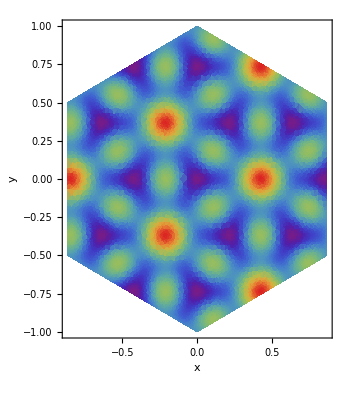

```mathematica
DensityPlot[Sum[nRnasnareauf0AB[x,y,1.5/180*Pi,30Sqrt[3],n],{n,2}],{x,-Sqrt[3]/2,Sqrt[3]/2},{y,-1,1},AxesLabel->Automatic, ColorFunction->"Rainbow",MaxRecursion->3, PlotRange->All,RegionFunction->Function[{x,y,z},-Sqrt[3]*x/3-1<y&&y<Sqrt[3]*x/3+1&&Sqrt[3]*x/3-1<y&&y<-Sqrt[3]*x/3+1],AspectRatio->Automatic]
```

```mathematica
hexagonarea=Integrate[Boole[-Sqrt[3]*x/3-1<y&&y<Sqrt[3]*x/3+1&&Sqrt[3]*x/3-1<y&&y<-Sqrt[3]*x/3+1],{x,-Sqrt[3]/2,Sqrt[3]/2},{y,-1,1}]
```

(3 √3)/2

```mathematica
t1=AbsoluteTime[];
hexAB[θ_,r_,n_]=FullSimplify[Integrate[nRnasnareauf0AB[x,y,θ,r,n]Boole[-Sqrt[3]*x/3-1<y&&y<Sqrt[3]*x/3+1&&Sqrt[3]*x/3-1<y&&y<-Sqrt[3]*x/3+1],{x,-Sqrt[3]/2,Sqrt[3]/2},{y,-1,1}]/hexagonarea]
t2=AbsoluteTime[];
Print["time used ",(t2-t1)/60," mins" ]
```

-((2 Cos[(2 n π)/3]+Cos[(4 n π)/3]) Sin[n π r √(2-2 Cos[θ])] (2 n π r √(2-2 Cos[θ]) Cos[n π r √(2-2 Cos[θ])]+Sin[n π r √(2-2 Cos[θ])]))/(6 n^2 π^2 r^2 (-1+Cos[θ]))

time used 0.693917788 mins

```mathematica
ToMatlab[hexAB[theta,r,n]]
```

(-1/6).*n.^(-2).*pi.^(-2).*r.^(-2).*(2.*cos((2/3).*n.*pi)+cos(( ...
  4/3).*n.*pi)).*((-1)+cos(theta)).^(-1).*sin(n.*pi.*r.*(2+(-2).* ...
  cos(theta)).^(1/2)).*(2.*n.*pi.*r.*(2+(-2).*cos(theta)).^(1/2).* ...
  cos(n.*pi.*r.*(2+(-2).*cos(theta)).^(1/2))+sin(n.*pi.*r.*(2+(-2).* ...
  cos(theta)).^(1/2)));